```mathematica
A DsixTools Program
This notebook shows how to introduce SMEFT input values in DsixTools directly.
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Start DsixTools

```mathematica
Needs["DsixTools`"]
```

DsixTools 1.0

by Alejandro Celis, Javier Fuentes-Martin, Avelino Vicente and Javier Virto

Reference: arXiv:1704.XXXXX

Website: https://dsixtools.github.io/

This program is free software: you can redistribute it and/or modify it under the terms of the GNU General Public License as published by the Free Software Foundation, either version 3 of the License, or any later version.

## Generate input values

## Options

```mathematica
LOWSCALE=100;
HIGHSCALE=10000;
```

```mathematica
CPV=0;
ReadRGEs=1;
RGEsMethod=1;
ExportRGEs=0;
UseRGEsSM=1;
exportSMEFTrunner=0;
exportEWmatcher=0;
exportWETrunner=0;
inputWCsType=1;
```

## SM parameters

```mathematica
Init[g]=0.4;
Init[gp]=0.7;
Init[gs]=0.9;
```

```mathematica
Init[λ]=0.1;
Init[m2]=8000;
```

```mathematica
Init[GU[1,1]]=1.23231*10^-5;
Init[GU[1,2]]=-1.64215*10^-3;
Init[GU[1,3]]=5.90635*10^-3;
Init[GU[2,1]]=2.84527*10^-6;
Init[GU[2,2]]=7.10724*10^-3;
Init[GU[2,3]]=-4.18547*10^-2;
Init[GU[3,1]]=4.65426*10^-8;
Init[GU[3,2]]=3.08758*10^-4;
Init[GU[3,3]]=0.994858;
```

```mathematica
Init[GD[1,1]]=2.70195*10^-5;
Init[GD[1,2]]=0;
Init[GD[1,3]]=0;
Init[GD[2,1]]=0;
Init[GD[2,2]]=5.51888*10^-4;
Init[GD[2,3]]=0;
Init[GD[3,1]]=0;
Init[GD[3,2]]=0;
Init[GD[3,3]]=2.403012*10^-2;
```

```mathematica
Init[GE[1,1]]=2.93766*10^-6;
Init[GE[1,2]]=0;
Init[GE[1,3]]=0;
Init[GE[2,1]]=0;
Init[GE[2,2]]=6.07422*10^-4;
Init[GE[2,3]]=0;
Init[GE[3,1]]=0;
Init[GE[3,2]]=0;
Init[GE[3,3]]=1.02157*10^-2;
```

```mathematica
Init[θ]=0;
Init[θp]=0;
Init[θs]=0;
```

## Wilson coefficients

```mathematica
(* Only the non-zero WCs should be provided *)
```

```mathematica
Init[LL[1,1,1,2]]=0.4;
```

## Create input values

```mathematica
(* We also save the input values in input files *)
```

```mathematica
WriteAndReadInputFiles["Options.dat","WCsInput.dat","SMInput.dat"];
```

Input: SMEFT Wilson coefficients

## Load SMEFTrunner module

```mathematica
LoadModule["SMEFTrunner"]
```

SMEFTrunner

DsixTools module for the RGE running of the Standard Model Effective Theory

## Use SMEFTrunner module

```mathematica
LoadBetaFunctions;
```

Loading SMEFT β functions

```mathematica
RunRGEsSMEFT;
```

Running

Running finished!

## Results after SMEFTrunner

```mathematica
(* We find the position of Subscript[(Subscript[C, ll]), 1112] in Parameters *)
FindParameterSMEFT[LL[1,1,1,2]]
```

{202}

```mathematica
outSMEFTrunner[[202]]/.t->tHIGH
outSMEFTrunner[[202]]/.t->tLOW
```

0.4

0.37026

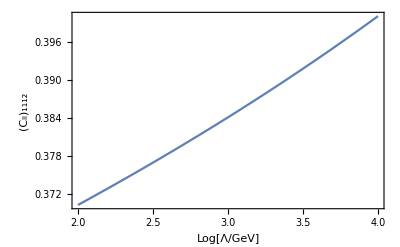

```mathematica
(* Wilson coefficients *)
plotWC=Plot[outSMEFTrunner[[202]],{t,tLOW,tHIGH},Frame->True,Axes->False,PlotRange->{{tLOW,tHIGH},Automatic},FrameLabel->{"Log[Λ/GeV]","(C_ll)_1112",None,None}]
```

```mathematica
(* Finally, one can also export the results to a file *)
```

```mathematica
ExportSMEFTrunner;
```